# Notebook for : On the geometry of curves and conformal geodesics in the Mobius space by Magliaro, Mari & Rigoli

Geoff Cope
University of Utah
                                                                                                             𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
May 7, 2021

```mathematica
(* 
Look up references 15 and 20 !!!!
*)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Paper

```mathematica
Hyperlink["On the geometry of curves and conformal geodesics in the Mobius space by Magliaro, Mari & Rigoli",
"https://arxiv.org/abs/1003.5776"]
```

[On the geometry of curves and conformal geodesics in the Mobius space by Magliaro, Mari & Rigoli](https://arxiv.org/abs/1003.5776)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 228 Kb

{Utilities`CleanSlate`,VariationalMethods`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y]-> dy , 
Dt[z]-> dz ,  
Dt[τ]-> dτ , 
Dt[θ] ->dθ, 
Dt[ϕ] ->dϕ,
Dt[η] ->dη, 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓏] -> d𝓏,
Dt[T]-> dT , 
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[τ]→dτ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
M /: Dt[M] = 0 ;  (* Mass of Schwarzschild is constant *) (* We use M for mass and m for null vector *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Conformal Curvatures μ1 and μ2

```mathematica
Clear[eq1]
eq1 = { 
μ1'[s] + 3 μ2[s] μ2'[s] == 0 , 
μ2''[s] == μ2[s]^3+ 2 μ1[s] μ2[s]
} ;
eq1 // TableForm
```

μ1'[s]+3 μ2[s] μ2'[s]==0
μ2''[s]==2 μ1[s] μ2[s]+μ2[s]^3

```mathematica
Clear[q2d]
q2d = 
 {μ1[s],μ2[s]}
```

{μ1[s],μ2[s]}

```mathematica
Clear[ics2d]
ics2d = { 
μ1[0] == 1 , 
μ2[0] == 3 , 
μ2'[0] == 4
} ;
ics2d // TableForm
```

μ1[0]==1
μ2[0]==3
μ2'[0]==4

```mathematica
Clear[solution2D]
solution2D = 
Flatten[NDSolve[ Flatten[{eq1 ,  ics2d}] , q2d , {s ,0,1}]]
```

{μ1[s]→InterpolatingFunction[…][s],μ2[s]→InterpolatingFunction[…][s]}

```mathematica
Clear[eq2]
eq2 = { 
μ1'[s] + 3 μ2[s] μ2'[s] == 0 , 
μ2''[s] == μ2[s]^3+ 2 μ1[s] μ2[s] + μ2[s] μ3[s]^2 , 
2 μ2'[s] μ3[s] + μ2[s] μ3'[s] == 0 
} ;
eq2 // TableForm
```

μ1'[s]+3 μ2[s] μ2'[s]==0
μ2''[s]==2 μ1[s] μ2[s]+μ2[s]^3+μ2[s] μ3[s]^2
2 μ3[s] μ2'[s]+μ2[s] μ3'[s]==0

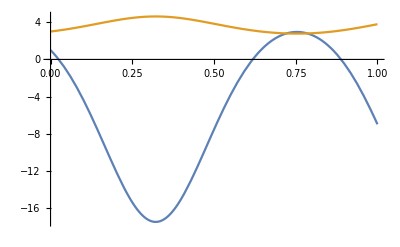

```mathematica
Plot[ Evaluate[ q2d  /. solution2D ]  , {s,0,1} ]
```

## Conformal Curvatures μ1, μ2 and μ3

```mathematica
Clear[q3d]
q3d = 
 {μ1[s],μ2[s],μ3[s]}
```

{μ1[s],μ2[s],μ3[s]}

```mathematica
Clear[ics3d]
ics3d = { 
μ1[0] == 1 , 
μ2[0] == 3 , 
μ2'[0] == 4 , 
μ3[0] == 5  
} ;
ics3d // TableForm
```

μ1[0]==1
μ2[0]==3
μ2'[0]==4
μ3[0]==5

```mathematica
Clear[solution3D]
solution3D = 
Flatten[NDSolve[ Flatten[{eq2 ,  ics3d}] ,q3d , {s ,0,1}]]
```

{μ1[s]→InterpolatingFunction[…][s],μ2[s]→InterpolatingFunction[…][s],μ3[s]→InterpolatingFunction[…][s]}

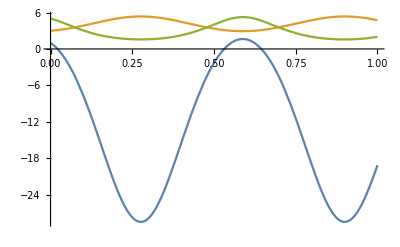

```mathematica
Plot[ Evaluate[ q3d  /. solution3D ]  , {s,0,1} ]
```